```mathematica
reversePoints[a_]:=Module[{aux},aux=a;For[i=1,i≤Length[points],i++,aux[[i,1]]=-a[[i,1]]];aux]
```

```mathematica
L=20;a=1;
```

```mathematica
points={{5.0,10},{5.101020514433644,11.0},{5.41742430504416,12.0},{6.0,13.0},{7.0,14.0},{8.0,14.582575694955839},{9.0,14.898979485566356},{10,15.0}};
```

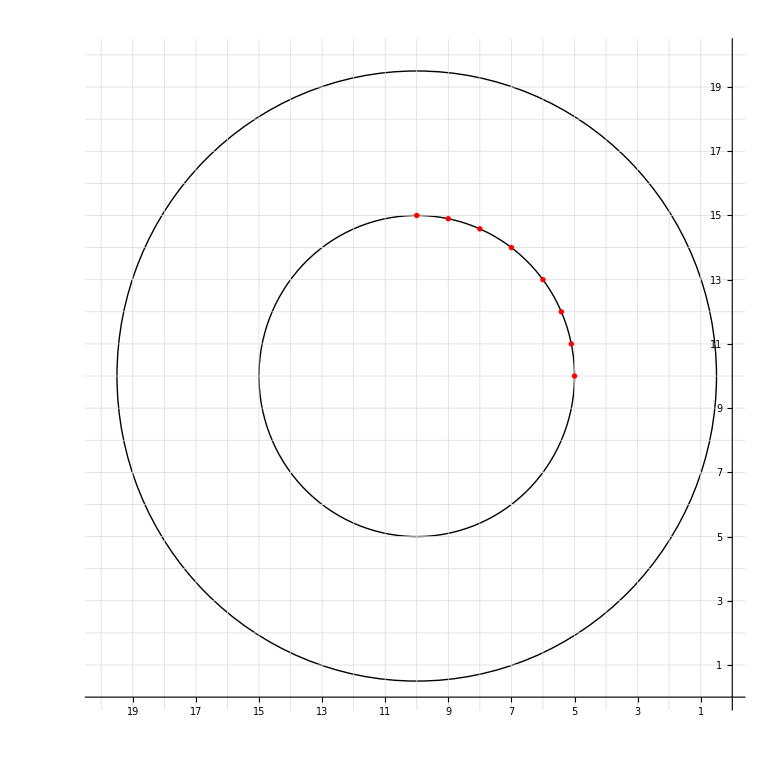

```mathematica
Graphics[{Circle[{-L/2,L/2},(L-a)/2],Circle[{-L/2,L/2},5a],{PointSize->0.005,Red, Point[reversePoints[points]]}},GridLines->{Table[i,{i,-L,0}],Table[i,{i,0,L}]},Axes->True,AxesOrigin->{0,0},PlotRange->{{-L-0.1,0},{0,L+0.1}},Ticks->{Table[{-i,i},{i,1,L}],Table[{i,i},{i,1,L}]}]
```